```mathematica
<<Local`SrednickiInit`
```

10.1) Use eq.(9.41) of problem 9.5 to rederive eq.(10.9).

```mathematica
DefPrint["e811",Δ[x[m,i]-x[n,i]]->IntegralOp[{k[o,i]},1/(2 π)^4 Exp[I k[o,i](x[m,i]-x[n,i])]/(k^2+m^2-I ϵ)]];
DefPrint["e934",Subscript[ϕ, In][x_,t_]->(ⅇ^(ⅈ t Subscript[H, 0])).ϕ[x,0].ⅇ^(-ⅈ t Subscript[H, 0])
];
Print["Spatial Fourier transform:",
tmp=ϕ[x,0]->IntegralOp[{k[n,space@i]},Exp[I k[n,space@i] x]ϕ[k[n,space@i]]],Imply;
tmp=Map[Exp[I Subscript[H, 0] t].#.Exp[-I Subscript[H, 0] t]&,tmp];Imply,
sub=e934[[1]]->tmp[[2]]
];
DefPrint["e941a",
⟨0|.T.ϕ[Subscript[x, n],Subscript[t, n]].ϕ[Subscript[x, -1+n],Subscript[t, -1+n]].ϕ[Subscript[x, 2],Subscript[t, 2]].ϕ[Subscript[x, 1],Subscript[t, 1]].ϕ[Subscript[x, 0],Subscript[t, 0]].|0⟩->1/⟨∅|.T.(ⅇ^(-ⅈ IntegralOp[{x},Subscript[ℋ, In][x]])).|∅⟩⟨∅|.T.Subscript[ϕ, In][Subscript[x, n],Subscript[t, n]].Subscript[ϕ, In][Subscript[x, -1+n],Subscript[t, -1+n]].Subscript[ϕ, In][Subscript[x, 2],Subscript[t, 2]].Subscript[ϕ, In][Subscript[x, 1],Subscript[t, 1]].Subscript[ϕ, In][Subscript[x, 0],Subscript[t, 0]].(ⅇ^(-ⅈ IntegralOp[{x},Subscript[ℋ, In][x]])).|∅⟩];

Print["→ ",tmp=e941a[[2]]/.sub;
tmp=UniqueIntVars3[tmp,{k}],
"\nSince ⟨ ∅|H_0->0 we add Exp[I H_0∞]",Yield,
tmp=tmp//.Exp[a_].Exp[b_]:>Exp[Simplify[a+b]];
tmp=tmp//.Exp[a_].IntegralOp[b_,c_]->IntegralOp[b,Exp[a] c]/.IntegralOp[a_,b_].IntegralOp[a_,c_]->IntegralOp[a,b c];
tmp=tmp[[1]]->(tmp[[2]]/.T->T.Exp[I Subscript[H, 0] ∞]);Imply;

];
"Unfinished."
```

e811: Δ[x_mi^mi-x_ni^ni]→IntegralOp[{k_oi^oi},(ⅇ^(ⅈ k_oi^oi (x_mi^mi-x_ni^ni)))/(16 π^4 (k^2+m^2-ⅈ ϵ))]

e934: ϕ_In[x_,t_]→ⅇ^(ⅈ t H_0).ϕ[x,0].ⅇ^(-ⅈ t H_0)

Spatial Fourier transform:ϕ[x,0]→IntegralOp[{k_ni^ni},ⅇ^(ⅈ x k_ni^ni) ϕ[k_ni^ni]]
⇒ ϕ_In[x_,t_]→ⅇ^(ⅈ t H_0).IntegralOp[{k_ni^ni},ⅇ^(ⅈ x k_ni^ni) ϕ[k_ni^ni]].ⅇ^(-ⅈ t H_0)

e941a: ⟨0|.T.ϕ[x_n,t_n].ϕ[x_(-1+n),t_(-1+n)].ϕ[x_2,t_2].ϕ[x_1,t_1].ϕ[x_0,t_0].|0⟩→⟨∅|.T.ϕ_In[x_n,t_n].ϕ_In[x_(-1+n),t_(-1+n)].ϕ_In[x_2,t_2].ϕ_In[x_1,t_1].ϕ_In[x_0,t_0].ⅇ^(-ⅈ IntegralOp[{x},ℋ_In[x]]).|∅⟩/⟨∅|.T.ⅇ^(-ⅈ IntegralOp[{x},ℋ_In[x]]).|∅⟩

→ ⟨∅|.T.ⅇ^(ⅈ H_0 t_n).IntegralOp[{k_(1i)^(1i)},ⅇ^(ⅈ x_n k_(1i)^(1i)) ϕ[k_(1i)^(1i)]].ⅇ^(-ⅈ H_0 t_n).ⅇ^(ⅈ H_0 t_(-1+n)).IntegralOp[{k_(2i)^(2i)},ⅇ^(ⅈ x_(-1+n) k_(2i)^(2i)) ϕ[k_(2i)^(2i)]].ⅇ^(-ⅈ H_0 t_(-1+n)).ⅇ^(ⅈ H_0 t_2).IntegralOp[{k_(3i)^(3i)},ⅇ^(ⅈ x_2 k_(3i)^(3i)) ϕ[k_(3i)^(3i)]].ⅇ^(-ⅈ H_0 t_2).ⅇ^(ⅈ H_0 t_1).IntegralOp[{k_(4i)^(4i)},ⅇ^(ⅈ x_1 k_(4i)^(4i)) ϕ[k_(4i)^(4i)]].ⅇ^(-ⅈ H_0 t_1).ⅇ^(ⅈ H_0 t_0).IntegralOp[{k_(5i)^(5i)},ⅇ^(ⅈ x_0 k_(5i)^(5i)) ϕ[k_(5i)^(5i)]].ⅇ^(-ⅈ H_0 t_0).ⅇ^(-ⅈ IntegralOp[{x},ℋ_In[x]]).|∅⟩/⟨∅|.T.ⅇ^(-ⅈ IntegralOp[{x},ℋ_In[x]]).|∅⟩
Since ⟨ ∅|H_0->0 we add Exp[I H_0∞]
→ Null

Unfinished.

10.2) Write down the Feynman rules for the complex scalar ﬁeld of prob- 
lem 9.3. Remember that there are two kinds of particles now (which 
we can think of as positively and negatively charged), and that your 
rules must have a way of distinguishing them. Hint: the most direct 
approach requires two kinds of arrows: momentum arrows (as dis- 
cussed in this section) and what we might call “charge” arrows (as 
discussed in problem 9.3). Try to ﬁnd a more elegant approach that 
requires only one kind of arrow. 

The rules can be modified for the comples scalar field by laying out the diagram on a space-time grid where the two fields represent particle and anti-particle.  External particles would have momentum propagating (pointing) forward in time; and external anti-particles would have momentum propagating (pointing) backward in time.  The vertex with factor is i λ Z_λ consists of 4 lines, 2 incoming and 2 outgoing.  This rule is patterned after the electron-positron diagrams.

10.3) Consider a complex scalar ﬁeld ϕ that interacts with a real scalar
ﬁeld χ via L1 = gχϕ † ϕ . Use a solid line for the ϕ propagator and
a dashed line for the χ propagator. Draw the vertex (remember the
arrows!), and ﬁnd the associated vertex factor.

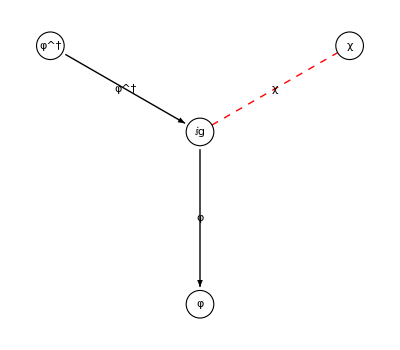

```mathematica
GraphPlot[{1->6,6->2,6->3},EdgeRenderingFunction->(Switch[Last[#2],
6,{Black, Arrow[#1,.1],Inset[Text["φ^†"],Mean[#1],Background->White]},2,{Black, Arrow[#1,.1],Inset[Text["φ"],Mean[#1],Background->White]},
3,{Red,Dashed,Line[#1],Black,Inset[Text["χ"],Mean[#1],Background->White]},_,{Red,Dashed,Line[#1],Black,Inset[Text[Last[#2]],Mean[#1],Background->White]}]&),
VertexRenderingFunction->(
Switch[#2,
1,{White,EdgeForm[Black],Disk[#,.08],Black,Text["φ^†",#1]},
2,{White,EdgeForm[Black],Disk[#,.08],Black,Text["φ",#1]},
3,{White,EdgeForm[Black],Disk[#,.08],Black,Text["χ",#1]},
6,{White,EdgeForm[Black],Disk[#,.08],Black,Text["ⅈg",#1]}]

&)
]
```

10.4) Consider a real scalar ﬁeld with L1 = 1/2 gϕ ∂µ ϕ ∂µ ϕ. Find the associ-
ated vertex factor.

```mathematica
DefPrint["p92L0",Subscript[ℒ, 0]->-1/2 PartialD[φ[x[n]],μ]PartialD[φ[x[n]],ν]guu[μ,ν]
-1/2 m^2 φ[x[n]]φ[x[n]]
];
DefPrint["e96",Z->Exp[I IntegralOp[{x[n]},Subscript[ℒ, 1][1/I δOp[J[x[n]]]]]].Subscript[Z, 0]];
DefPrint["e97",Subscript[Z, 0]->Exp[I/2 IntegralOp[{x[a],x[b]},J[x[a]]. Δ[x[a]-x[b]].J[x[b]]]]];
DefPrint["p104",Subscript[ℒ, 1][φ_]->HoldForm[1/2 g.φ.(PartialD[φ,μ].PartialD[φ,ν].guu[μ,ν])]];
t96a=e96/.p104/.SuperDagger[δOp[a_]]->δOp[SuperDagger[a]]/.SuperDagger[J[a_]]->SuperDagger[J][a]//ReleaseHold
```

p92L0: ℒ_0→-1/2 (φ[x_n^n])_(,μ) (φ[x_n^n])_(,ν) g_μν^μν-1/2 m^2 φ[x_n^n]^2

e96: Z→ⅇ^(ⅈ IntegralOp[{x_n^n},ℒ_1[-ⅈ δOp[J[x_n^n]]]]).Z_0

e97: Z_0→ⅇ^(1/2 ⅈ IntegralOp[{x_a^a,x_b^b},J[x_a^a].Δ[x_a^a-x_b^b].J[x_b^b]])

p104: ℒ_1[φ_]→1/2 g.φ.((φ)_(,μ).(φ)_(,ν).guu[μ,ν])

Z→ⅇ^(ⅈ IntegralOp[{x_n^n},1/2 g.(-ⅈ δOp[J[x_n^n]]).(-ⅈ (δOp[J[x_n^n]])_(,μ)).(-ⅈ (δOp[J[x_n^n]])_(,ν)).g_μν^μν]).Z_0

```mathematica
ordered={xPartialD[_,_],IntegralOp[_,_],δOp[_],J[_],SuperDagger[J][_],Δ[_],guu[_,_],Subscript[Z, 0],Z0SEP}
IntDotInt2Int2= IntegralOp[a_,intgA_]. IntegralOp[b_,intgB_]:>IntegralOp[Flatten[{a,b}],intgA.intgB];
nV=3;
nP=3;
t96=t96a/.Exp[Y_]->Normal[Series[Exp[Y],{Y,0,nV}]]//.Power[IntegralOp[a_,b_],n_]:>DotPower[IntegralOp[a,b],n];
t96=UniqueIntVars3[%,{x}](*Z*);
t96=t96//.IntDotInt2Int2;
t96=t96/.PartialD->xPartialD(*avoid unexpected PartialD action in patterns*)

t97=e97/.Exp[Y_]->Normal[Series[Exp[Y],{Y,0,nP}]]/.Power[IntegralOp[a_,b_],n_]:>DotPower[IntegralOp[a,b],n];

t97=UniqueIntVars3[t97,{x}]//.IntDotInt2Int2 (*Z0*)
t97=t97/.IntegralOp[a_,b_]->IntegralOp[a,Z0SEP.b];
```

{xPartialD[_,_],IntegralOp[_,_],δOp[_],J[_],J^*[_],Δ[_],g___^__,Z_0,Z0SEP}

Z→(ⅈ IntegralOp[{x_6^6},1/2 g.(-ⅈ δOp[J[x_6^6]]).(-ⅈ xPartialD[δOp[J[x_6^6]],μ]).(-ⅈ xPartialD[δOp[J[x_6^6]],ν]).g_μν^μν]).Z_0+(-1/2 IntegralOp[{x_1^1,x_2^2},(1/2 g.(-ⅈ δOp[J[x_1^1]]).(-ⅈ xPartialD[δOp[J[x_1^1]],μ]).(-ⅈ xPartialD[δOp[J[x_1^1]],ν]).g_μν^μν).(1/2 g.(-ⅈ δOp[J[x_2^2]]).(-ⅈ xPartialD[δOp[J[x_2^2]],μ]).(-ⅈ xPartialD[δOp[J[x_2^2]],ν]).g_μν^μν)]).Z_0+(-1/6 ⅈ IntegralOp[{x_3^3,x_4^4,x_5^5},(1/2 g.(-ⅈ δOp[J[x_3^3]]).(-ⅈ xPartialD[δOp[J[x_3^3]],μ]).(-ⅈ xPartialD[δOp[J[x_3^3]],ν]).g_μν^μν).(1/2 g.(-ⅈ δOp[J[x_4^4]]).(-ⅈ xPartialD[δOp[J[x_4^4]],μ]).(-ⅈ xPartialD[δOp[J[x_4^4]],ν]).g_μν^μν).(1/2 g.(-ⅈ δOp[J[x_5^5]]).(-ⅈ xPartialD[δOp[J[x_5^5]],μ]).(-ⅈ xPartialD[δOp[J[x_5^5]],ν]).g_μν^μν)]).Z_0+Z_0

Z_0→1+1/2 ⅈ IntegralOp[{x_11^11,x_12^12},J[x_11^11].Δ[x_11^11-x_12^12].J[x_12^12]]-1/8 IntegralOp[{x_1^1,x_2^2,x_3^3,x_4^4},J[x_1^1].Δ[x_1^1-x_2^2].J[x_2^2].J[x_3^3].Δ[x_3^3-x_4^4].J[x_4^4]]-1/48 ⅈ IntegralOp[{x_5^5,x_6^6,x_7^7,x_8^8,x_9^9,x_10^10},J[x_5^5].Δ[x_5^5-x_6^6].J[x_6^6].J[x_7^7].Δ[x_7^7-x_8^8].J[x_8^8].J[x_9^9].Δ[x_9^9-x_10^10].J[x_10^10]]

```mathematica
t96/.t97;
tmp=
dotRetain[ordered,UniqueIntVars3[%,{x}]]//.IntDotInt2Int2;
tmpSave=tmp
Length[tmpSave[[2]]]
```

Z→1+ⅈ IntegralOp[{x_55^55},1/2 ⅈ g δOp[J[x_55^55]].xPartialD[δOp[J[x_55^55]],μ].xPartialD[δOp[J[x_55^55]],ν].g_μν^μν]-1/2 IntegralOp[{x_56^56,x_57^57},-1/4 g^2 δOp[J[x_56^56]].xPartialD[δOp[J[x_56^56]],μ].xPartialD[δOp[J[x_56^56]],ν].g_μν^μν.δOp[J[x_57^57]].xPartialD[δOp[J[x_57^57]],μ].xPartialD[δOp[J[x_57^57]],ν].g_μν^μν]+1/2 ⅈ IntegralOp[{x_58^58,x_59^59},Z0SEP.J[x_58^58].Δ[x_58^58-x_59^59].J[x_59^59]]-1/2 IntegralOp[{x_1^1,x_2^2,x_3^3},(1/2 ⅈ g δOp[J[x_1^1]].xPartialD[δOp[J[x_1^1]],μ].xPartialD[δOp[J[x_1^1]],ν].g_μν^μν).Z0SEP.J[x_2^2].Δ[x_2^2-x_3^3].J[x_3^3]]-1/6 ⅈ IntegralOp[{x_60^60,x_61^61,x_62^62},-1/8 ⅈ g^3 δOp[J[x_60^60]].xPartialD[δOp[J[x_60^60]],μ].xPartialD[δOp[J[x_60^60]],ν].g_μν^μν.δOp[J[x_61^61]].xPartialD[δOp[J[x_61^61]],μ].xPartialD[δOp[J[x_61^61]],ν].g_μν^μν.δOp[J[x_62^62]].xPartialD[δOp[J[x_62^62]],μ].xPartialD[δOp[J[x_62^62]],ν].g_μν^μν]-1/4 ⅈ IntegralOp[{x_16^16,x_17^17,x_18^18,x_19^19},(-1/4 g^2 δOp[J[x_16^16]].xPartialD[δOp[J[x_16^16]],μ].xPartialD[δOp[J[x_16^16]],ν].g_μν^μν.δOp[J[x_17^17]].xPartialD[δOp[J[x_17^17]],μ].xPartialD[δOp[J[x_17^17]],ν].g_μν^μν).Z0SEP.J[x_18^18].Δ[x_18^18-x_19^19].J[x_19^19]]-1/8 IntegralOp[{x_63^63,x_64^64,x_65^65,x_66^66},Z0SEP.J[x_63^63].Δ[x_63^63-x_64^64].J[x_64^64].J[x_65^65].Δ[x_65^65-x_66^66].J[x_66^66]]-1/8 ⅈ IntegralOp[{x_4^4,x_5^5,x_6^6,x_7^7,x_8^8},(1/2 ⅈ g δOp[J[x_4^4]].xPartialD[δOp[J[x_4^4]],μ].xPartialD[δOp[J[x_4^4]],ν].g_μν^μν).Z0SEP.J[x_5^5].Δ[x_5^5-x_6^6].J[x_6^6].J[x_7^7].Δ[x_7^7-x_8^8].J[x_8^8]]+1/12 IntegralOp[{x_34^34,x_35^35,x_36^36,x_37^37,x_38^38},(-1/8 ⅈ g^3 δOp[J[x_34^34]].xPartialD[δOp[J[x_34^34]],μ].xPartialD[δOp[J[x_34^34]],ν].g_μν^μν.δOp[J[x_35^35]].xPartialD[δOp[J[x_35^35]],μ].xPartialD[δOp[J[x_35^35]],ν].g_μν^μν.δOp[J[x_36^36]].xPartialD[δOp[J[x_36^36]],μ].xPartialD[δOp[J[x_36^36]],ν].g_μν^μν).Z0SEP.J[x_37^37].Δ[x_37^37-x_38^38].J[x_38^38]]+1/16 IntegralOp[{x_20^20,x_21^21,x_22^22,x_23^23,x_24^24,x_25^25},(-1/4 g^2 δOp[J[x_20^20]].xPartialD[δOp[J[x_20^20]],μ].xPartialD[δOp[J[x_20^20]],ν].g_μν^μν.δOp[J[x_21^21]].xPartialD[δOp[J[x_21^21]],μ].xPartialD[δOp[J[x_21^21]],ν].g_μν^μν).Z0SEP.J[x_22^22].Δ[x_22^22-x_23^23].J[x_23^23].J[x_24^24].Δ[x_24^24-x_25^25].J[x_25^25]]-1/48 ⅈ IntegralOp[{x_67^67,x_68^68,x_69^69,x_70^70,x_71^71,x_72^72},Z0SEP.J[x_67^67].Δ[x_67^67-x_68^68].J[x_68^68].J[x_69^69].Δ[x_69^69-x_70^70].J[x_70^70].J[x_71^71].Δ[x_71^71-x_72^72].J[x_72^72]]+1/48 IntegralOp[{x_9^9,x_10^10,x_11^11,x_12^12,x_13^13,x_14^14,x_15^15},(1/2 ⅈ g δOp[J[x_9^9]].xPartialD[δOp[J[x_9^9]],μ].xPartialD[δOp[J[x_9^9]],ν].g_μν^μν).Z0SEP.J[x_10^10].Δ[x_10^10-x_11^11].J[x_11^11].J[x_12^12].Δ[x_12^12-x_13^13].J[x_13^13].J[x_14^14].Δ[x_14^14-x_15^15].J[x_15^15]]+1/48 ⅈ IntegralOp[{x_39^39,x_40^40,x_41^41,x_42^42,x_43^43,x_44^44,x_45^45},(-1/8 ⅈ g^3 δOp[J[x_39^39]].xPartialD[δOp[J[x_39^39]],μ].xPartialD[δOp[J[x_39^39]],ν].g_μν^μν.δOp[J[x_40^40]].xPartialD[δOp[J[x_40^40]],μ].xPartialD[δOp[J[x_40^40]],ν].g_μν^μν.δOp[J[x_41^41]].xPartialD[δOp[J[x_41^41]],μ].xPartialD[δOp[J[x_41^41]],ν].g_μν^μν).Z0SEP.J[x_42^42].Δ[x_42^42-x_43^43].J[x_43^43].J[x_44^44].Δ[x_44^44-x_45^45].J[x_45^45]]+1/96 ⅈ IntegralOp[{x_26^26,x_27^27,x_28^28,x_29^29,x_30^30,x_31^31,x_32^32,x_33^33},(-1/4 g^2 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].g_μν^μν.δOp[J[x_27^27]].xPartialD[δOp[J[x_27^27]],μ].xPartialD[δOp[J[x_27^27]],ν].g_μν^μν).Z0SEP.J[x_28^28].Δ[x_28^28-x_29^29].J[x_29^29].J[x_30^30].Δ[x_30^30-x_31^31].J[x_31^31].J[x_32^32].Δ[x_32^32-x_33^33].J[x_33^33]]-1/288 IntegralOp[{x_46^46,x_47^47,x_48^48,x_49^49,x_50^50,x_51^51,x_52^52,x_53^53,x_54^54},(-1/8 ⅈ g^3 δOp[J[x_46^46]].xPartialD[δOp[J[x_46^46]],μ].xPartialD[δOp[J[x_46^46]],ν].g_μν^μν.δOp[J[x_47^47]].xPartialD[δOp[J[x_47^47]],μ].xPartialD[δOp[J[x_47^47]],ν].g_μν^μν.δOp[J[x_48^48]].xPartialD[δOp[J[x_48^48]],μ].xPartialD[δOp[J[x_48^48]],ν].g_μν^μν).Z0SEP.J[x_49^49].Δ[x_49^49-x_50^50].J[x_50^50].J[x_51^51].Δ[x_51^51-x_52^52].J[x_52^52].J[x_53^53].Δ[x_53^53-x_54^54].J[x_54^54]]

16

```mathematica
DefPrint["e1012",Δ[a_]->IntegralOp[{k[α,i]},1/(2 π)^4 Exp[ⅈ k[α,i]a]/(k^2+m^2)]
]
distributePartialD=xPartialD[a_,b_]:>If[Head[a]===Plus,Map[xPartialD[#,b]&,a],xPartialD[a,b]];
subZero[exp_]:=Module[{},exp//.xPartialD[J[a_],J[b_]]:>DiracDelta[a-b]/.xPartialD[xPartialD[xPartialD[Δ[a_],m_],n_],J[b_]]->0//.xPartialD[xPartialD[Δ[a_],m_],J[b_]]->0//.
xPartialD[Δ[__],J[_]]->0 //.xPartialD[Δ[0],_]->0//.xPartialD[a_Integer,_]->0//.xPartialD[δOp[_],_]->0//.xPartialD[guu[_,_],_]->0//.xPartialD[(J[_]|DiracDelta[_]|Δ[0]),b_]->0
];

(*extracts δOp terms from expression*)
coefδOp[exp_]:=Module[{dotPos=Position[exp,Dot],i,tmp,term,termpos,opPos,opterms,repl={}},(*allow for plain and sum of Dot[] *)
For[i=1,i≤Length[dotPos],i++,termpos=Most[dotPos[[i]]];
If[termpos==={},tmp=exp,
tmp=Extract[exp,termpos]];
(*assume δOp are first terms in Dot function*)
opPos=Position[tmp,δOp];
opterms=OCoef[Apply[Dot,Extract[tmp,Map[{First[#]}&,opPos]]]];
tmp=opterms ReplacePart[tmp,Map[{First[#]}&,opPos]->1];
AppendTo[repl,termpos->tmp];
];
If[termpos==={},tmp,
ReplacePart[exp,repl]//Simplify]
];
```

e1012: Δ[a_]→IntegralOp[{k_αi^αi},(ⅇ^(ⅈ a k_αi^αi))/(16 (k^2+m^2) π^4)]

```mathematica
seqterm=Sequence[2,-2];
tmpterm=tmpSave[[seqterm]]
tmpint=tmpterm=tmpterm/.MoveIntOut/.IntegralOp[a_,b_]:>IntegralOp[a,dotRetain[ordered,b]];
tmp=tmpterm/.IntegralOp[a_,b_]->b;
coef=tmp/.HoldPattern[Dot[_]]->1;
tmp=tmp/coef;(*remove coefficient*)
tmpv=tmp/.Z0SEP.b__->1 (*Verticies in Dot[]*)
tmpp=tmp/.a__.Z0SEP->1 (*Propagators in Dot[]*)
tmpint1=tmpint;
tmpv1=tmpv;
tmpp1=tmpp;
coef1=1;
opterms=Position[tmpv1,δOp[_]];
Print[nv=Length[opterms],":",np=Length[Position[tmpp1,J[_]]]];
```

1/96 ⅈ IntegralOp[{x_26^26,x_27^27,x_28^28,x_29^29,x_30^30,x_31^31,x_32^32,x_33^33},(-1/4 g^2 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].g_μν^μν.δOp[J[x_27^27]].xPartialD[δOp[J[x_27^27]],μ].xPartialD[δOp[J[x_27^27]],ν].g_μν^μν).Z0SEP.J[x_28^28].Δ[x_28^28-x_29^29].J[x_29^29].J[x_30^30].Δ[x_30^30-x_31^31].J[x_31^31].J[x_32^32].Δ[x_32^32-x_33^33].J[x_33^33]]

δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].g_μν^μν.δOp[J[x_27^27]].xPartialD[δOp[J[x_27^27]],μ].xPartialD[δOp[J[x_27^27]],ν].g_μν^μν

J[x_28^28].Δ[x_28^28-x_29^29].J[x_29^29].J[x_30^30].Δ[x_30^30-x_31^31].J[x_31^31].J[x_32^32].Δ[x_32^32-x_33^33].J[x_33^33]

6:6

```mathematica
tmpint1=tmpint
tmpv1=tmpv;
tmpp1=tmpp;
coef1=1;
opterms=Position[tmpv1,δOp[_]];
Print[nv=Length[opterms],":",np=Length[Position[tmpp1,J[_]]]];
(*loop around until no more δOp*)
icnt=0;pcnt=20;
While[nv<=np&&Length[opterms]>0&&icnt++<2,
opterms=Position[tmpv1,δOp[_]];
Print[icnt,":opterms:0: ",opterms,"<",tmpv1];
(*need ending logic*)
If[Length[opterms]==1,(*only one term*)
termpos=opterms//Last;
term=tmpv1
,
termpos=opterms//Last;
termpos=termpos//First;
term=tmpv1[[termpos]]
];
Print[termpos,":term: ",term];
If[icnt==pcnt,Print[icnt,":v0: ",tmpv1]];
List[ops=term,"\nterm: ",ops,"\ndvar: ",dvar=Extract[ops,Position[ops,(J[_]|SuperDagger[J][_])]][[1]]];
If[icnt==pcnt,Print[icnt,":p1:0: ",tmpx=tmpp1]];
(*derivative of J[_] ** only Dot terms differentiated*)
(*tmp=tmpp1/.Dot[a_]:>xPartialDDot[Dot[a],dvar];*)
tmp=xPartialDDot[tmpp1,dvar];
tmp=subZero[tmp];If[icnt==pcnt,Print[icnt,":1:tmp OK: ",tmp]];
(*insert back into term*)
tmp=ReplacePart[term,Position[term,δOp[_]]->tmp];
tmp=tmp/.xPartialD->xPartialDDot;
tmp=subZero[tmp];
(*new integrand*)
If[termpos=!={},
tmp=ReplacePart[tmpv1,termpos->tmp]
];
(****)
tmp=tmpint1/.IntegralOp[a_,b_]->IntegralOp[a,tmp];
If[icnt==pcnt,Print[icnt,":1:tmp OK: ",tmp]];
(*evaluate integral*)
tmp=tmp//.distributeInt;
tmp=findEvalIntDelta[tmp,x[4]];
tmpint1=gatherIntFast[UniformIntVar[tmp]];
(*find new tmpv1,tmpp1*)
tmpp1=tmpint1/.IntegralOp[a_,b_]->b;
If[icnt==pcnt,Print[icnt,":p1 9: ",tmpp1,"\nv1: ",tmpv1]];
tmp=coefδOp[tmpp1];
If[icnt==pcnt,Print[icnt,":tmp 9: ",tmp]];
tmpv1=tmp/.b_ OCoef[a_]->a;
tmpp1=tmp/.OCoef[a_]->1;
(*eliminate δOp from tmpp1*)
If[icnt==pcnt,Print[icnt,": p1 A: ",tmpp1,"\nv1 A: ",tmpv1]];
]
subZero[tmpint1]/.Dot->Times
```

IntegralOp[{x_26^26,x_27^27,x_28^28,x_29^29,x_30^30,x_31^31,x_32^32,x_33^33},-1/384 ⅈ g^2 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].g_μν^μν.δOp[J[x_27^27]].xPartialD[δOp[J[x_27^27]],μ].xPartialD[δOp[J[x_27^27]],ν].g_μν^μν.Z0SEP.J[x_28^28].Δ[x_28^28-x_29^29].J[x_29^29].J[x_30^30].Δ[x_30^30-x_31^31].J[x_31^31].J[x_32^32].Δ[x_32^32-x_33^33].J[x_33^33]]

6:6

1:opterms:0: {{1},{2,1},{3,1},{5},{6,1},{7,1}}<δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].g_μν^μν.δOp[J[x_27^27]].xPartialD[δOp[J[x_27^27]],μ].xPartialD[δOp[J[x_27^27]],ν].g_μν^μν

7:term: xPartialD[δOp[J[x_27^27]],ν]

2:opterms:0: {{1,2,1},{1,2,2,1},{1,2,3,1},{1,2,4},{1,2,5,1},{2,2,1},{2,2,2,1},{2,2,3,1},{2,2,4},{2,2,5,1},{3,2,1},{3,2,2,1},{3,2,3,1},{3,2,4},{3,2,5,1},{4,2,1},{4,2,2,1},{4,2,3,1},{4,2,4},{4,2,5,1},{5,2,1},{5,2,2,1},{5,2,3,1},{5,2,4},{5,2,5,1},{6,2,1},{6,2,2,1},{6,2,3,1},{6,2,4},{6,2,5,1}}<3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_28^28]].xPartialD[δOp[J[x_28^28]],μ]+3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_29^29]].xPartialD[δOp[J[x_29^29]],μ]+3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_30^30]].xPartialD[δOp[J[x_30^30]],μ]+3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_31^31]].xPartialD[δOp[J[x_31^31]],μ]+3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_32^32]].xPartialD[δOp[J[x_32^32]],μ]+3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_33^33]].xPartialD[δOp[J[x_33^33]],μ]

6:term: 3 δOp[J[x_26^26]].xPartialD[δOp[J[x_26^26]],μ].xPartialD[δOp[J[x_26^26]],ν].δOp[J[x_33^33]].xPartialD[δOp[J[x_33^33]],μ]

$Aborted

IntegralOp[{x_26^26,x_28^28,x_29^29,x_30^30,x_31^31,x_32^32,x_33^33},0]

```mathematica
M
Position[%,IntegralOp];
tmp1>>"saveSrednicki.10.tmp1"
tmp2=findEvalIntDelta[tmp1];
tmp2>>"saveSrednicki.10.tmp2"
M1
tmp3=UniformIntVar1[tmp2];
tmp3>>"saveSrednicki.10.tmp3"
M2
tmp4=tmp3/.Null->0/.Dot->Times//Expand;
tmp4>>"saveSrednicki.10.tmp4"
M3
tmp5=gatherIntFast[tmp4];
tmp5>>"saveSrednicki.10.tmp5"
Position[tmp5,IntegralOp];
tmp6=tmp5/.Δ[-x[a_,i]+x[b_,i]]->Δd[M[a]M[b] ]/.Δd[M[a_] M[b_]]->Δ[x[a,i]- x[b,i]];
(*sign of argument of Δ not important*)
tmp6>>"saveSrednicki.10.tmp6"
tmp7=RearrangeIntJArg[tmp6];
```